{0.0507662,-0.0351094,0.0381265,-0.226546,0.132128}

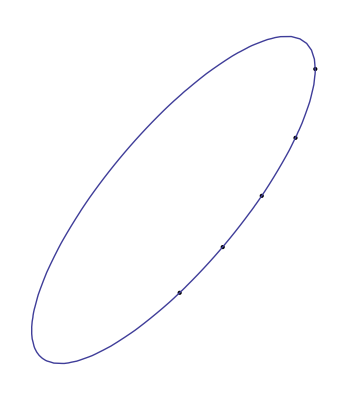

```mathematica
x = {5.764,6.286,6.759,7.168,7.408};
y = {0.648,1.202,1.823,2.526,3.36};
A =Transpose[{x^2,2x y, y^2, 2x, 2y } ];
b = 0*y - 1;
a=LinearSolve[A, b]
fig1 = Graphics[Point[Transpose[{x,y}]]];
fig2 = ContourPlot[a[[1]] x^2+2a[[2]]x  y+ a[[3]] y^2+2a[[4]]x+2a[[5]]y==-1,{x,3.9,7.5},{y,-0.3,3.9}];
Show[fig1,fig2]
```